```mathematica
gy1[r_,xi_,d_]:=1/Cosh[r/xi]*SphericalBesselJ[0,2*Pi*r/d]
```

```mathematica
gy2[r_,xi_,d_,rc_]:=(Exp[-r/xi]-rc/xi*Exp[-r/rc])/(1-rc/xi)*SphericalBesselJ[0,2*Pi*r/d]
```

```mathematica
gy3[r_,xi_,d_,rm_]:=Module[{k0=2*Pi/d, a=xi/rm},a*(a+1)/(a-1)^2(Exp[-r/xi]+Exp[-a*r/xi]/a-4*xi/(r*(a^2-1))*(Exp[-r/xi]-Exp[-a*r/xi]))*SphericalBesselJ[0,k0*r]]
```

```mathematica
gy3[1,2,1,rm]
```

(xi (1+xi/rm) (ⅇ^(-r/xi)+(ⅇ^(-r/rm) rm)/xi-(4 (-ⅇ^(-r/rm)+ⅇ^(-r/xi)) xi)/(r (1-rc/xi) (-1+xi^2/rm^2))) SphericalBesselJ[0,(2 π r)/d])/(rm (-1+xi/rm)^2)

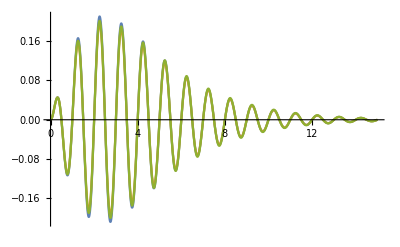

```mathematica
Plot[{gy1[r,2,1]*r^2,gy2[r,2,1,1]*r^2,gy3[r,2,1,0.5]*r^2},{r,0,15}]
```